# Roseller Periodic Orbits Lots of them

### Walk Through

We want to find periodic orbits of the Rosseler system.  It is going to help us understand the “strange attractor”.

We know we need to use Newtons Method to match points on the Poincare section.

We found a periodic orbit with winding number 2 near the near-miss orbit (which we found earlier) below.

```mathematica
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
TMax=15.2;
{w,wMax}={0,2};
yP={-4.656808847594422,0.0,0.01940187976631838};
ySol = NDSolveValue[{
y'[t]==f[StdParams][y[t]], y[0]==yP},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1,
"EventAction":>If[++w≥wMax,tEnd=t;"StopIntegration"]
}]
Show[ParametricPlot3D[ySol[t],{t,0, tEnd},PlotRange->All],Graphics3D[CutPlane]]
```

InterpolatingFunction[…]

-Graphics3D-

We want to find more periodic orbits.

```mathematica
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
TMax=17.5;
yP={-9,0.0,0.01940187976631838};
ySol = NDSolveValue[{
y'[t]==f[StdParams][y[t]], y[0]==yP},y,{t,0, TMax}]
Show[ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All],Graphics3D[CutPlane]]
```

InterpolatingFunction[…]

-Graphics3D-

Here is the code from the winding number 2 computation we wrote to try to compute the change and sensitivity on the section.  We need to make it work more generally!

```mathematica
G3[{y1_,y3_}]:=Module[{yP,JP,w=0,wMax=3,y,J,t,TMax=32},
{yP,JP}=Quiet[Reap[NDSolveValue[{
y'[t]==f[StdParams][y[t]], y[0]=={y1,0,y3},
J'[t]==df[StdParams][y[t]].J[t], J[0]==IdentityMatrix[3]},{},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1,
"EventAction":>If[++w≥wMax,Sow[{y[t],J[t]}];"StopIntegration"]
}]]⟦2,1,1⟧];
{yP⟦{1,3}⟧,JP⟦{1,3},{1,3}⟧}]
G3[{-9,0.01940187976631838}]
```

{{-8.7947,0.0138394},{{-2.92999,0.199001},{-0.00235985,0.000160577}}}

The Newton computation step we iterated to fix a near miss is
	y_(k+1)=y_k+(dg(y_k)-Id_2)^-1.(y_k-g(y_k))
If it gets stuck then you have an accurate answer.

```mathematica
y0={-4.743977711024888,0.019234252282450195}
{g0,dg0}=G3[y0];
y1=y0+LinearSolve[dg0-IdentityMatrix[2],y0-g0]

{g1,dg1}=G3[y1];
y2=y1+LinearSolve[dg1-IdentityMatrix[2],y1-g1]

{g2,dg2}=G3[y2];
y3=y2+LinearSolve[dg2-IdentityMatrix[2],y2-g2]

{g3,dg3}=G3[y3];
y4=y3+LinearSolve[dg3-IdentityMatrix[2],y3-g3]

{g4,dg4}=G3[y4];
y5=y4+LinearSolve[dg4-IdentityMatrix[2],y4-g4]

{g5,dg5}=G3[y5];
y6=y5+LinearSolve[dg5-IdentityMatrix[2],y5-g5]

{g6,dg6}=G3[y6];
y7=y6+LinearSolve[dg6-IdentityMatrix[2],y6-g6]

{g7,dg7}=G3[y7];
y8=y7+LinearSolve[dg7-IdentityMatrix[2],y7-g7]

g7-y7
```

{-4.74398,0.0192343}

{-5.25164,0.0174637}

{-5.34819,0.0181076}

{-5.35588,0.0181609}

{-5.3559,0.0181654}

{-5.3559,0.0181654}

{-5.3559,0.0181654}

«2 more identical outputs»

{4.17444×10^-14,-6.48787×10^-16}

We can and should automate this Newton process.

```mathematica
NewtonStep[{y_,NormRes_}]:= Module[{g,dg,yNew},
{g,dg}=G3[y];
yNew=y+LinearSolve[dg-IdentityMatrix[2],y-g];
{yNew, Norm[yNew-g]}
]
MaxIter=34;
NestWhileList[NewtonStep, {y0,∞}, (#[[2]]>10^-12)&,1, MaxIter]
NestWhile[NewtonStep, {y0,∞}, (#[[2]]>10^-12)&,1, MaxIter]
```

{{{-4.74398,0.0192343},∞},{{-5.25164,0.0174637},2.51631},{{-5.34819,0.0181076},0.283796},{{-5.35588,0.0181609},0.0182693},{{-5.3559,0.0181654},0.0000496425},{{-5.3559,0.0181654},1.92139×10^-7},{{-5.3559,0.0181654},7.47882×10^-10},{{-5.3559,0.0181654},2.915×10^-12},{{-5.3559,0.0181654},2.93099×10^-14}}

{{-5.3559,0.0181654},2.93099×10^-14}

The next thing to do is to try to find a whole lot of near miss points.  I am going to do this by running our ODE solver for a long time and catching the points where it crosses our section y_2==0.  Any points that nearly repeat are near miss points!

## Automated Near-Misses

```mathematica
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
TMax=10^3;
yP={-9,0.0,0.01940187976631838};
MessyData=Reap[NDSolveValue[{
y'[t]==f[StdParams][y[t]], y[0]==yP},{},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1,
"EventAction":>Sow[y[t]]}]];
TidyData=MessyData⟦2,1,All,{1,3}⟧;
{y1Data,y3Data}=TidyDataᵀ;
TabView[{
"y_1-y_3 Plane"->ListPlot[ TidyData,PlotLabel->Length[TidyData],AxesLabel->{"y_1","y_3"}],
"y_1"->ListPlot[ y1Data,PlotLabel->Length[TidyData],AxesLabel->{"y_1","y_3"}],
"y_3"->ListPlot[ y3Data,PlotLabel->Length[TidyData],AxesLabel->{"y_1","y_3"}]
}
]
```

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

123

One way to look for near misses in the data is to search the following matrix for non-diagonal small values!

```mathematica
MatrixPlot[
Table[ 
If[i≤j,y1Data⟦i⟧-y1Data⟦j⟧,1],
{i,Length[y1Data]},{j, Length[y1Data]}],
PlotLegends->Automatic
]
```

-Graphics-

Another way would be to search the following 1D plots for small values!

```mathematica
TabView[Table[
ListLogPlot[ Abs[y1Data-RotateLeft[y1Data,i]],PlotRange->All,PlotLabel->StringForm["Shift=``",i]],
{i, Min[20,Length[y1Data]]}]]
```

1234567891011121314151617181920

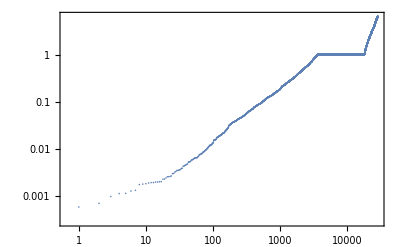

```mathematica
Distances=Table[ 
If[i<j,Abs[y1Data⟦i⟧-y1Data⟦j⟧],1],
{i,Length[y1Data]},{j, Length[y1Data]}];
ListLogLogPlot[Sort[Flatten[Distances]],PlotRange->All,GridLines->Automatic,Frame->True]
```